# Spin-1

We focus on the simplest illustration studied in this work; the three-level case.

```mathematica
Needs["SUN`"]; (* https://github.com/kercl/sun *)
```

```mathematica
Np= 100 ;(* Number of atoms *)
```

## 1 Local operators and their collective representation

First we define the Spin-1 and SU(3) generators matrices (Gell-Mann) in the fundamental representation. Then, we compute the corresponding matrix representations of the SU(3) generators on the totally symmetric subspace of the Np atoms, MatSU3, with the SUN  package.

```mathematica
MatSpin=LieAlgebraBasisMatrices[Irrep[2]][[1]]; (* Spin-1 matrices *)
MatGM=N[LieAlgebraBasisMatrices[Irrep[1,0]][[1]]]; (* Gell-Mann SU(3) matrices *)
```

```mathematica
MatSU3=N[LieAlgebraBasisMatrices[Irrep[Np,0]][[1]]] ; (*Collective representation of SU(3) matrices*)
dim=Dimensions[MatSU3][[2]]; (*And its dimension*)
```

For a arbitrary local operator o, we compute the collective matrix representation Ir[o] := O

```mathematica
Ir[o_]:=Sum[2*Tr[o.MatGM[[a]]]*MatSU3[[a]],{a,1,First[Dimensions[MatSU3]]}]+Np*Tr[o]*IdentityMatrix[dim, SparseArray]/First[Dimensions[MatGM[[1]]]];
```

The projector onto outcome m of a local observable o.  Will be used in the following to compute the magnetic-sublevel single atom projectors from the Spin-1 observables.

```mathematica
Pro[o_,m_]:=Sum[KroneckerDelta[m,Eigensystem[o][[1]][[a]]]*KroneckerProduct[Eigensystem[o][[2]][[a]]*,Eigensystem[o][[2]][[a]]],{a,1,First[Dimensions[o]]}];
Proj[o_,m_]:=Pro[o,m]/Tr[Pro[o,m]];
```

## a) Separable bound beta

As set of local operators, we will use spin-1 and magnetic-sublevel single atom projectors onto sublevel 0 for three orthogonal directions {x,y,z}

```mathematica
o={{MatSpin[[1]], Proj[MatSpin[[1]],0]},{MatSpin[[2]], Proj[MatSpin[[2]],0]},{MatSpin[[3]], Proj[MatSpin[[3]],0]}};
```

We proceed by computing the separable bound, beta,  from the local operators o by maximizing betapsi over single atom states as indicated in the paper

```mathematica
betapsi[o_,psi_]:=Total[Table[ First[First[Abs[(psi.o[[a,m]].psi†)/(psi.psi†)]^2]],{a,1,3},{m,1,2}],2];betaTmp=Table[betapsi[o,{RandomVariate[CircularUnitaryMatrixDistribution[3]][[1]]}],{i,1,500000}];
Max[betaTmp]
```

1.49959

Here we propose to estimate the optimal beta by just sampling random three-level vectors from the U(3) Haar measure.  A  More sophisticated approach is implemented in “find_betabound.py” where we maximize from a random vector using the methods integrated in scipy.  From which we conclude,

```mathematica
beta=1.5;
```

## 2 The three-level spinor Bose gas model

We define the Hamiltonian of the spin-1 Bose gas

H(c,q)=c[J]^2/N+qQ^(z)

 in whose ground state (GS) in the J_z=0  sector quantum entanglement will be probed

```mathematica
J2= Ir[MatSpin[[1]]].Ir[MatSpin[[1]]]+Ir[MatSpin[[2]]].Ir[MatSpin[[2]]]+Ir[MatSpin[[3]]].Ir[MatSpin[[3]]]; (* Total spin *)
Qz=Ir[MatSpin[[3]].MatSpin[[3]]]; (* Quadrupole *)

IdxRed=Flatten[Position[Re[Normal[Diagonal[Ir[MatSpin[[3]]]]]],_?(Abs[#]<0.01&)]]; (* We only consider the basis elements with J_z=0 *)
H[c_,q_]:= (c*J2/Np+q*Qz)[[IdxRed, IdxRed]];

GS[H_]:=First[Eigenvectors[H+Norm[H]*IdentityMatrix[Dimensions[H][[1]]],-1]]; (* Ground state *)
EV[O_,S_]:=Re[Tr[KroneckerProduct[Conjugate[S],S].O]];  (* Expectation value of the GS with respect collective operator O *)
```

## a) Quantum data

The next step is to gather the data from the model in the form of one-body vector m and two-body correlation matrix C
 
m = <Ir[o]>/N
C = < Ir[o] Ir[o]^t-Ir[oo^t]>/(N(N-1))

for each direction {x,y,z}.

```mathematica
m[state_]:=Flatten[Table[EV[Ir[o[[a,m]]][[IdxRed,IdxRed]],state]/Np,{a,1,3},{m,1,Dimensions[o][[2]]}]];
of=Flatten[o,1];
Cor[state_]:= Table[  EV[(Ir[of[[k]]].Ir[of[[r]]]+Ir[of[[r]]].Ir[of[[k]]]-Ir[of[[k]].of[[r]]+of[[r]].of[[k]]]) [[IdxRed,IdxRed]], state]/(2*Np*(Np-1))  ,{k,1,Dimensions[of][[1]]},{r,1,Dimensions[of][[1]]}];
```

## 3 Data-driven entanglement detection

We consider the modified correlation which enter linearly in the central result ‘ single entanglement witness to test them all’’ of the paper considering a block-diagonal form of the correlations along each direction.

```mathematica
Ctilde[Cor_,m_]:=Np*(Cor-KroneckerProduct[m*,m]);
CtildeXYZ[Cor_,m_]:= DiagonalMatrix[Unevaluated@{Ctilde[Cor,m][[{1,2},{1,2}]],Ctilde[Cor,m][[{3,4},{3,4}]],Ctilde[Cor,m][[{5,6},{5,6}]]}]//ArrayFlatten
```

We compute the optimal value of the witness given the bound beta as well as the corresponding projector.

```mathematica
(* Sum of negative eigenvalues of C *) 
Pscalar[C_]:=Sum[(1-Round[HeavisideTheta[Eigenvalues[C][[a]]]])*Eigenvalues[C][[a]],{a,1,First[Dimensions[C,1]]}];
(* Optimal projector *)
PP[C_]:=Sum[(1-Round[HeavisideTheta[Eigenvalues[C][[a]]]])*KroneckerProduct[Eigenvectors[C][[a]]*,Eigenvectors[C][[a]]],{a,1,First[Dimensions[C,1]]}];
(* Entanglement witness  *)
W[Cor_,m_]:=Pscalar[CtildeXYZ[Cor,m]]-Tr[Cor]+beta;
```

Now we move on to test our algorithm. First we consider the GS with c=1, q=1 to obtain:

```mathematica
c= 1;
q= 1;
```

```mathematica
state=GS[H[c,q]];
ms=m[state];
Cors=Cor[state];
```

```mathematica
W[Cors, ms]
```

-0.601591

The negative value indicates violation of the entanglement witness and therefore quantum entanglement is required to reproduce the data {C,m } within a quantum theory.

```mathematica
Re[PP[CtildeXYZ[Cors, ms]]]//  MatrixForm
```

(1. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 1. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 1. | -1.7244×10^-14
0. | 0. | 0. | 0. | -1.7244×10^-14 | 2.97355×10^-28)

Where the basis in which the the matrix is written is {j_x, n0_x, j_y, n0_y, j_z, n0_z}  where j_a is the spin (dipole) operator along direction a and n0_a is the projection to the Zeeman sublevel with zero spin projection along a (see definition of o). For unpolarized states, with this projector we infer an entanglement witness of the form Hfeas

```mathematica
Idred=IdentityMatrix[Length[IdxRed]];
NO2=(Ir[Proj[MatSpin[[1]],0]].Ir[Proj[MatSpin[[1]],0]] +Ir[Proj[MatSpin[[2]],0]].Ir[Proj[MatSpin[[2]],0]] +Ir[Proj[MatSpin[[3]],0]].Ir[Proj[MatSpin[[3]],0]])[[IdxRed, IdxRed]];
Hfeas[x_,y_]:= x*(J2[[IdxRed, IdxRed]]/Np-Idred)+y*(NO2/(Np*(Np-1))+((Np-3)/(2*(Np-1))-1)*Idred);
```

for x=-y=1, maximally violated in the SU(2) point, c=1 and q=0 . We chose the partition in x,y such that for x=1, y=0,  the expression is equivalent to the Vitagliano-Tóth criteria <J^2>>= N

For the ferromagnetic case, c=-1,  q=1 we find another witness violated:

```mathematica
c=-1;
q=1;
```

```mathematica
state=GS[H[c,q]];
ms=m[state];
Cors=Cor[state];
```

```mathematica
W[Cors, ms]
```

-0.310982

```mathematica
Re[PP[CtildeXYZ[Cors, ms]]]//  MatrixForm
```

(0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 1. | -2.10974×10^-16
0. | 0. | 0. | 0. | -2.10974×10^-16 | 4.45101×10^-32)

This time leading to an anisotropic witness in the dipolar space, since only the z component of the spin is projected.

## 4 Correlations’ feasible region

The feasible region in the correlation plane , <X> ,<Y>, as defined in Hfeas = xX+yY is obtained as the convex hull of the correlations <X> ,<Y> computed against the GS of Hfeas for a large range of {x,y}. For the present witness, the relevant boundary can be evaluated fixing x =	1.

```mathematica
Ndp=1000; (* Number of datapoints *)
```

```mathematica
x=1;
yvalues=N@Subdivide[-400,400,Ndp];

EVX=Table[EV[Hfeas[1,0],GS[Hfeas[x,yvalues[[y]]]]],{y,1,Ndp}];
EVY=Table[EV[Hfeas[0,1],GS[Hfeas[x,yvalues[[y]]]]],{y,1,Ndp}];
```

In this plane, the data reproduced by the GS of the spin-1 spinor model H[1,1] addressed previously is mapped to the point:

```mathematica
Xdata={EV[Hfeas[1,0],GS[H[1,1]]]}
Ydata ={EV[Hfeas[0,1],GS[H[1,1]]]}
```

{-0.108358}

{0.493234}

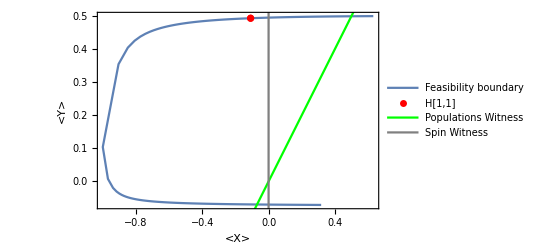

```mathematica
Show[ListLinePlot[Transpose@{EVX,EVY},Frame->True,FrameLabel->{"<X>","<Y>"},Axes->{False,False},PlotLegends->{"Feasibility boundary"}],
ListPlot[Transpose@{Xdata,Ydata},PlotStyle->Red,PlotLegends->{"H[1,1]"}],
Plot[x,{x,-1,1},PlotStyle->Green,PlotLegends->{"Populations Witness"}],
ListLinePlot[Transpose@{ConstantArray[0,3],N@Subdivide[-1,2,2]} ,PlotStyle->Gray,PlotLegends->{"Spin Witness"}]]
```

We indicated as well the two lines corresponding to the populations based witness x = -y =1 and the spin-based Vitagliano-Tóth witness.

The same procedure is to be carried out analogously with the remaining anisotropic witness.

This is used in the paper to compare the present witness with the Vitagliano-Tóth criteria, obtaining that the novel one is more robust in the region in which is obtained in the data-driven way from the ground state of the Bose gas.  Moreover, we obtain violation for the twin-Fock state c = 0, q = -1, which is not detected entanglement via spin-1 correlations.